```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nR[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in \Nalba_i \Nabla^i H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] ϕ'[r]
```

```mathematica
(*fVISC[r] = f^{VISC r}_notes*)
```

```mathematica
fVISC[r_]:=2 η ig[r][[1,1]]( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]])
```

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r])))/(r^3 (1+z'[r]^2)^(5/2))};
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r])))/(r^3 (1+z'[r]^2)^(5/2))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ig[r][[1,1]]( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
C1=1;
```

```mathematica
Solve[eqs[[2]]/.{r->Rmin}/.{z'[Rmin]->1/10,z''[Rmin]->0,z'''[Rmin]->0,z''''[Rmin]->0},σ[1]]
```

{{σ[1]→1/202 (201-40 √101)}}

```mathematica
bcs={
σ[Rmin]==1/202 (201-40 √101),
z'[Rmin]==1/10,z''[Rmin]==0,z'''[Rmin]==0,z''''[Rmin]==0
};
```

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
(*Boundary conditions to feed into the finite-element code*)
```

```mathematica
(*σ[Rmin] = sigma_r_const in variatinal_problem_bc_ring.py*)
```

```mathematica
N[1/202 (201-40 √101),20]
```

-0.99502487546948322183

```mathematica
(*z[Rmin] = z_r_const in variational_problem_bc_ring.py*)
```

```mathematica
z[r]/.{r->Rmin}/.sol
```

1.

```mathematica
(*z[Rmax]= z_R_const in variational_problem_bc_ring.py*)
```

```mathematica
z[r]/.{r->Rmax}/.sol
```

1.0990007696349066183303716066

```mathematica
(*n^i omega_i_{at r = Rmin} = omega_r_const in variational_problem_bc_ring.py*)
```

```mathematica
(Sum[{z'[r],0}[[i]]* nr[{r,θ}][[i]],{i,1,2}])/.repv/.sol/.{r->Rmin}
```

-0.099503719020998913567

```mathematica
(*n^i omega_i at r = Rmax = omega_R_const in variational_problem_bc_ring.py*)
```

```mathematica
(Sum[{z'[r],0}[[i]]* nR[{r,θ}][[i]],{i,1,2}])/.repv/.sol/.{r->Rmax}
```

0.095353866240961546555843199533

```mathematica
(*v[Rmin] = v_r_const in variational_problem_bc_ring.py*)
```

```mathematica
v[r]/.repv/.{r->Rmin}/.sol
```

0.9950371902099891356653

```mathematica
(*v^i n_i_{r = Rmax} = v_R_const in variational_problem_bc_ring.py *)
```

```mathematica
(Sum[{v[r],0}[[i]]* nR[{r,θ}][[j]] g[r][[i,j]],{i,1,2},{j,1,2}])/.repv/.sol/.{r->Rmax}
```

0.5

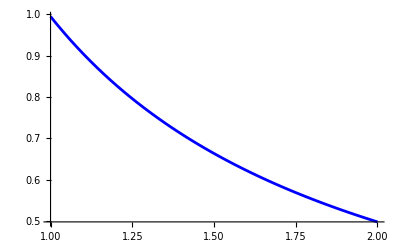

```mathematica
plotvexact=Plot[v[r]/.repv/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

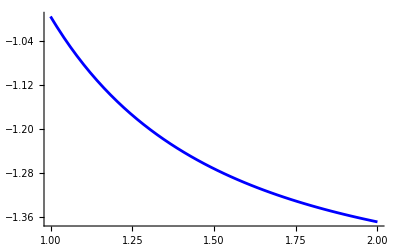

```mathematica
plotσexact=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

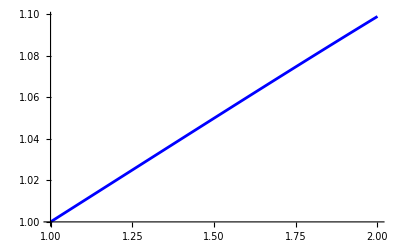

```mathematica
plotzexact=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

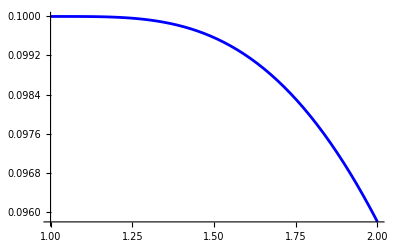

```mathematica
plotωexact=Plot[z'[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

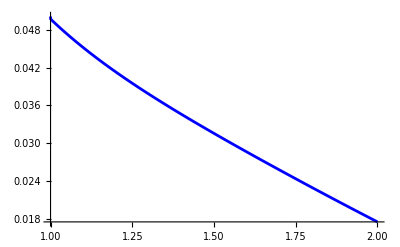

```mathematica
plotμexact=Plot[H[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
delta=1/100;
```

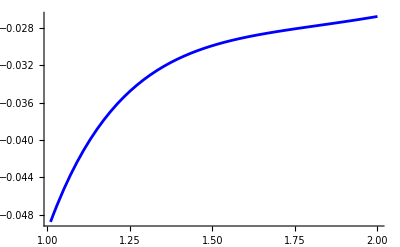

```mathematica
plotνexact=Plot[Evaluate[H'[r]/. sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

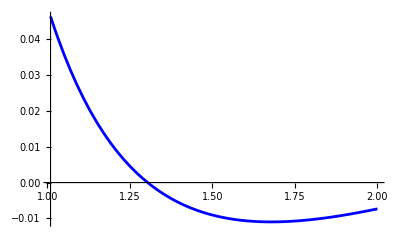

```mathematica
plotτexact=Plot[Evaluate[NablaNablaH[r]/. sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of v*)
```

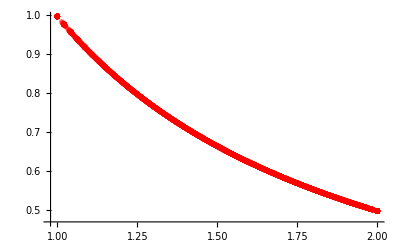

```mathematica
tabv=Import["~/Documents/finite_elements/steady-state-flow/solution/v.csv"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],Norm[{tabv[[i,1]],tabv[[i,2]]}]},{i,2,Length[tabv]}]
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

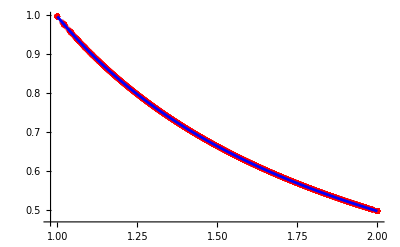

```mathematica
Show[plotvfe,plotvexact]
```

```mathematica
(*check of sigma*)
```

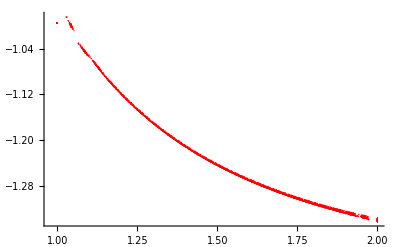

```mathematica
tabσ=Import["~/Documents/finite_elements/steady-state-flow/solution/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
plotσfe=ListPlot[tabσ,PlotRange->Full,PlotStyle->{PointSize->.002,Red,Opacity[1]}]
```

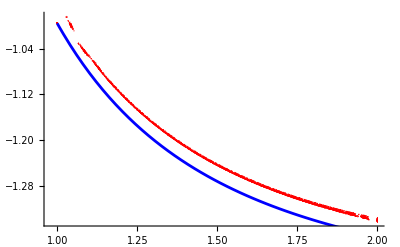

```mathematica
Show[plotσfe,plotσexact]
```

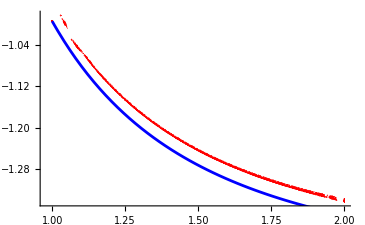
```mathematica
(*res = 0.05*)
-Graphics-;
```

```mathematica
(*res = 0.02*)
```

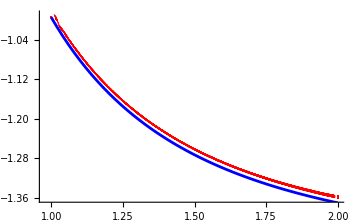
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.01*)
```

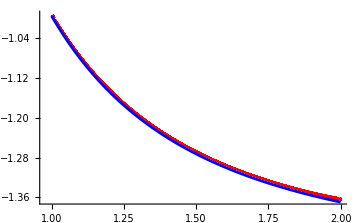
```mathematica
-Graphics-;
```

```mathematica
(*check of z*)
```

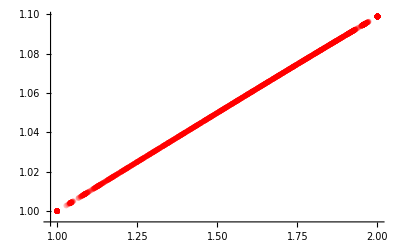

```mathematica
tabz=Import["~/Documents/finite_elements/steady-state-flow/solution/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,2,Length[tabz]}]
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

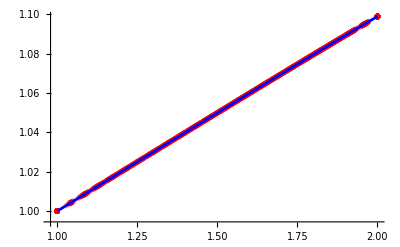

```mathematica
Show[plotzfe,plotzexact]
```

```mathematica
(*check of ω*)
```

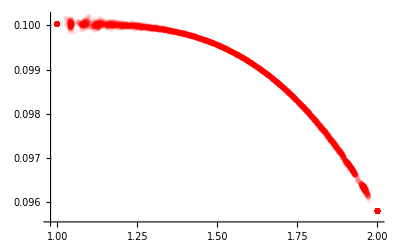

```mathematica
tabω=Import["~/Documents/finite_elements/steady-state-flow/solution/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],({tabω[[i,4]],tabω[[i,5]]}/Norm[{tabω[[i,4]],tabω[[i,5]]}]).{tabω[[i,1]],tabω[[i,2]]}},{i,2,Length[tabω]}]
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

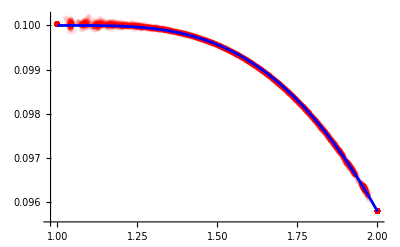

```mathematica
Show[plotωfe,plotωexact]
```

```mathematica
(*check of μ*)
```

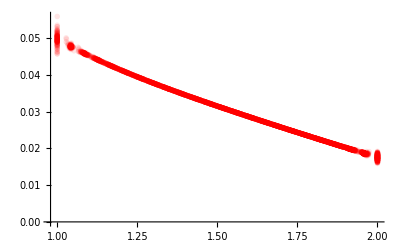

```mathematica
tabμ=Import["~/Documents/finite_elements/steady-state-flow/solution/mu.csv"];
tabμ=Table[{Norm[{tabμ[[i,2]],tabμ[[i,3]]}],tabμ[[i,1]]},{i,2,Length[tabμ]}]
plotμfe=ListPlot[tabμ,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

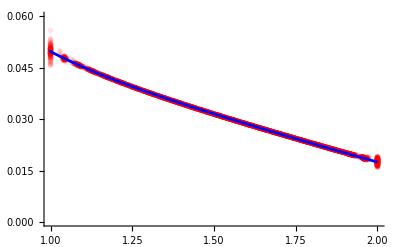

```mathematica
Show[plotμfe,plotμexact,PlotRange->{0,0.06}]
```

```mathematica
(*check nu*)
```

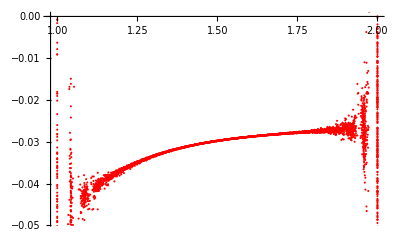

```mathematica
ν=Import["~/Documents/finite_elements/steady-state-flow/solution/nu.csv"];
ν=Table[{Sqrt[ν[[i,4]]^2+ν[[i,5]]^2],ν[[i,4]]/Sqrt[ν[[i,4]]^2+ν[[i,5]]^2] ν[[i,1]]+ν[[i,5]]/Sqrt[ν[[i,4]]^2+ν[[i,5]]^2] ν[[i,2]]},{i,2,Length[ν]}]
plotνnum=ListPlot[ν,PlotStyle->{Red,Opacity->1}]
```

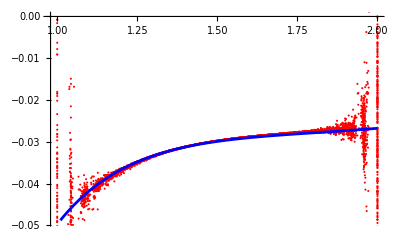

```mathematica
Show[plotνnum,plotνexact]
```

```mathematica
(*check τ*)
```

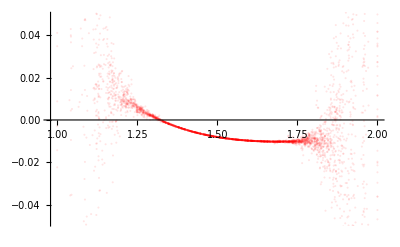

```mathematica
τnum=Import["~/Documents/finite_elements/steady-state-flow/solution/tau.csv"];
τnum=Table[{Sqrt[τnum[[i,2]]^2+τnum[[i,3]]^2],τnum[[i,1]]},{i,2,Length[τnum]}]
plotτnum=ListPlot[τnum,PlotStyle->{Red,Opacity->0.1}]
```

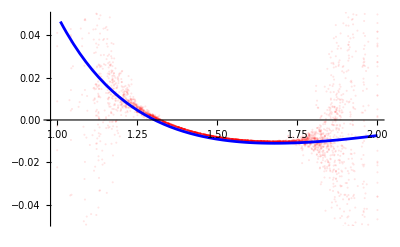

```mathematica
Show[plotτnum,plotτexact]
```

```mathematica
(*check of forces*)
```

```mathematica
(*normal forces*)
```

```mathematica
tabfeln=Import["~/Documents/finite_elements/steady-state-flow/solution/fel_n.csv"];
tabfeln=Table[{Norm[{tabfeln[[i,2]],tabfeln[[i,3]]}],tabfeln[[i,1]]},{i,2,Length[tabfeln]}]
```

```mathematica
tabflaplacen=Import["~/Documents/finite_elements/steady-state-flow/solution/flaplace.csv"];
tabflaplacen=Table[{Norm[{tabflaplacen[[i,2]],tabflaplacen[[i,3]]}],tabflaplacen[[i,1]]},{i,2,Length[tabflaplacen]}]
```

```mathematica
tabfviscn=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_n.csv"];
tabfviscn=Table[{Norm[{tabfviscn[[i,2]],tabfviscn[[i,3]]}],tabfviscn[[i,1]]},{i,2,Length[tabfviscn]}]
```

```mathematica
tabftotn=Table[{tabfviscn[[i,1]],tabfeln[[i,2]]+tabflaplacen[[i,2]]+tabfviscn[[i,2]]},{i,2,Length[tabfviscn]}]
```

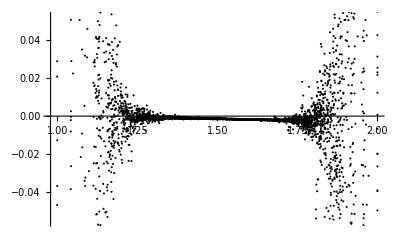

```mathematica
ListPlot[tabftotn,PlotStyle->Black]
```

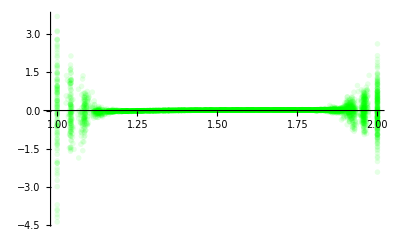

```mathematica
plotfeln=ListPlot[tabfeln,PlotRange->Full,PlotStyle->{PointSize->.01,Green,Opacity[0.1]}]
```

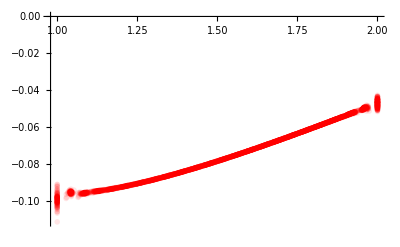

```mathematica
plotflaplacen=ListPlot[tabflaplacen,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

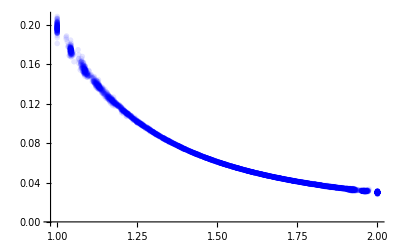

```mathematica
plotfviscn=ListPlot[tabfviscn,PlotRange->Full,PlotStyle->{PointSize->.01,Blue,Opacity[0.1]}]
```

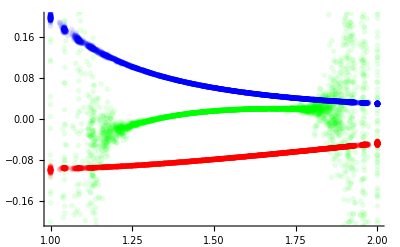

```mathematica
Show[plotfeln,plotflaplacen,plotfviscn,PlotRange->{-0.2,0.2}]
```

```mathematica
(*tangential forces*)
```